```mathematica
files = FileNames["*.tab"];
datas = Drop[Import[#], 1]&/@files;
ch1s=Transpose[{#[[All,1]],#[[All,2]]}]&/@datas;
ch2s=Transpose[{#[[All,1]],#[[All,3]]}]&/@datas;
data = Transpose[{ch1s, ch2s}];
filterdata = data[[ ;; 13]];
foehndata = data[[14 ;; ]];
```

```mathematica
fitrange={{0,0.0011},{0,0.0028},{0,0.0035},{0,0.0053},{0,0.012},{0,0.012},{0,0.012},{0,0.012}};
fitdata =Table[Select[filterdata[[i, 1]], #[[1]]≥ fitrange[[i,1]] && #[[1]]≤fitrange[[i,2]]&],{i,{1,2,3,4,8}}];
```

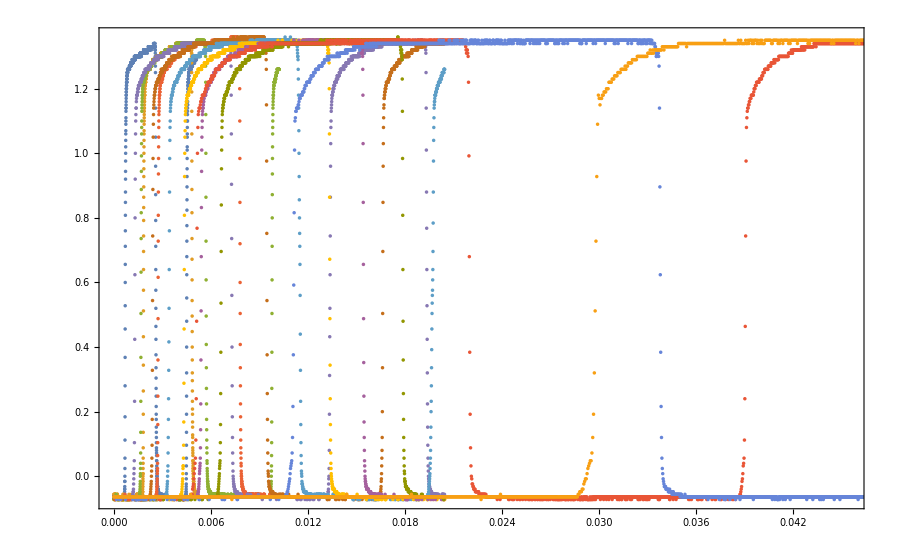

```mathematica
ListPlot[filterdata[[#,1]]&/@Range[13],ImageSize->900,Frame->True]
```

## nlm1

```mathematica
nlm= NonlinearModelFit[fitdata[[3]],{ a/(1+Exp[(-x+μ)/(σ*10^-3)])+b-Piecewise[{{0,x<μ},{ c Exp[-d x],x≥μ}}],a<10,b<0,b>-0.1,c>0,c<5,d>0,d<1000,σ>0,σ<0.1,μ<0.005,μ>0.004}, {{a,2},{b,-0.07},{μ,0.0043},{σ,0.03},{c,2},{d,500}}, x]
nlm["ParameterTable"]
```

## nlm2

```mathematica
n=4;
startval={{{a,1.23},{b,0},{μ,1},{σ,10},{c,0.11},{d,10}},
{{a,1.23},{b,0},{μ,1},{σ,10},{c,0.11},{d,10}},
{{a,1.23},{b,0},{μ,1},{σ,10},{c,0.11},{d,10}},
{{a,1.23},{b,0},{μ,2.7},{σ,10},{c,0.15},{d,1}}};
nlm= NonlinearModelFit[fitdata[[n]],
{a/(1+Exp[(-x+μ*10^-3)/(σ*10^-6)])+b-Piecewise[{{c,x<μ*10^-3},{ c Exp[-d*10^3 (x-μ*10^-3)],x≥μ*10^-3}}],
0.1<a,a<2,-1<b,b<1,0.5<μ,μ<3,0.1<σ,σ<100,0.001<c,c<10,1<d,d<100}, startval[[n]], x]
nlm["ParameterTable"]
```

FittedModel[0.0944538+1.24982/(1+ⅇ^(65876.2 («22»-x)))-(Piecewise[{{0.158231, x<0.00274439}, {0.158231 ⅇ^(-1192.2 (-«22»+x)), x≥0.00274439}, {0, True}}])]

FittedModel::constr: The property values {"ParameterTable"} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
a | 1.24982 | 0.00142575 | 876.605 | 1.52747562568×10^-1512
b | 0.0944538 | 0.00123512 | 76.4734 | 1.2394687918×10^-432
μ | 2.74439 | 0.000119477 | 22970. | 1.35252043246×10^-3008
σ | 15.18 | 0.102256 | 148.451 | 2.70764807419×10^-709
c | 0.158231 | 0.00120123 | 131.724 | 2.50994729548×10^-657
d | 1.1922 | 0.0280709 | 42.471 | 1.3174×10^-230

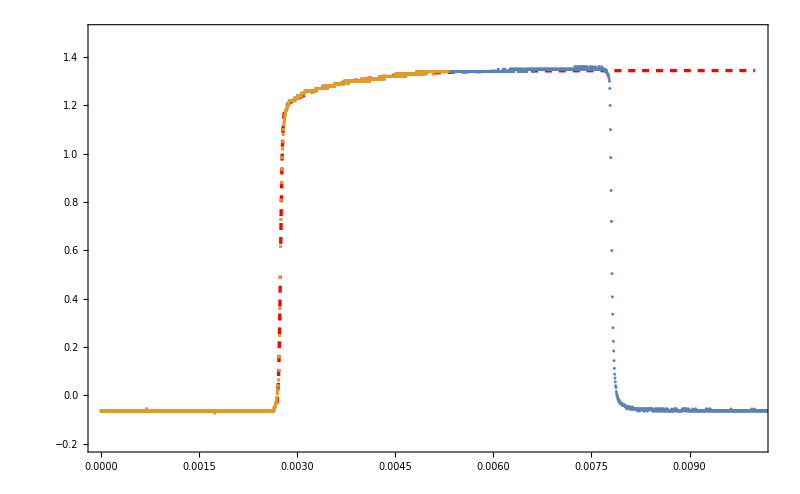

```mathematica
Show[Plot[Normal[nlm],{x,0,0.01},ImageSize->800,Frame->True,PlotRange->{-0.2,1.5},ImageSize->500,Frame->True, PlotStyle->{Red, Dashed,Thickness->0.003}],ListPlot[{filterdata[[n,1]],fitdata[[n]]},PlotMarkers->{Automatic,3}]]
```

```mathematica
Manipulate[Show[Plot[{Normal[nlm],a/(1+Exp[(-x+μ*10^-3)/(σ*10^-6)])+b-Piecewise[{{c,x<μ*10^-3},{ c Exp[-d (x-μ*10^-3)],x≥μ*10^-3}}]},{x,0,0.01},ImageSize->600,Frame->True,PlotRange->{-0.2,1.5},Frame->True, PlotStyle->{Red, Dashed,3}],ListPlot[{filterdata[[n,1]],fitdata[[n]]},PlotMarkers->{Automatic,1}]],{{a,1.23},0,5},{{b,0.05},-2,2},{{μ,1.8},0.7,3},{{σ,10},1,20},{{c,0.11},0,2},{{d,9300},0,10000}]
```

```mathematica
ListPlot[filterdata[[7,1]],ImageSize->700,Frame->True]
```

```mathematica
einsatz={{{0.0007778,1.186}},{{0.001905,1.179}},{{0.001759,1.175}},{{0.002808,1.169}},{{0.001421,1.16}},{{0.002485,1.158}},{{0.003456,1.143}},{{0.004395,1.13}},{{0.005459,1.119}},{{0.006711,1.112}},{{0.005196,1.115}},{{0.01114,1.097}},{{0.03011,1.161}}};
fallend={{{0.002593,0.6409}},{{0.004839,0.6786}},{{0.005703,0.6157}},{{0.007769,0.7189}},{{0.007306,0.7321}},{{0.009466,0.7529}},{{0.01147,0.7529}},{{0.01338,0.672}},{{0.01541,0.6945}},{{0.01786,0.6394}},{{0.02186,0.6795}},{{0.03376,0.6269}},{{0.08176,0.647}}};
```

{1.186,1.179,1.175,1.169,1.16,1.158,1.143,1.13,1.119,1.112,1.115,1.097,1.161}

{1.8152,2.934,3.944,4.961,5.885,6.981,8.014,8.985,9.951,11.149,16.664,22.62,51.65}

{{1.8152,1.186},{2.934,1.179},{3.944,1.175},{4.961,1.169},{5.885,1.16},{6.981,1.158},{8.014,1.143},{8.985,1.13},{9.951,1.119},{11.149,1.112},{16.664,1.115},{22.62,1.097},{51.65,1.161}}

{{1.8152,1.186},{2.934,1.179},{3.944,1.175},{4.961,1.169},{5.885,1.16},{6.981,1.158},{8.014,1.143},{8.985,1.13},{9.951,1.119},{11.149,1.112}}

FittedModel[1.09335+0.12 ⅇ^(-0.116905 x)]

FittedModel::constr: The property values {"ParameterTable"} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
a | 8.55393 | 8.7754 | 0.974762 | 0.362152
min | 1.09335 | 0.0606636 | 18.0231 | 4.00083×10^-7
amp | 0.12 | 0.0453137 | 2.64821 | 0.0330276

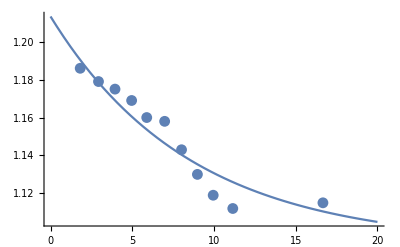

```mathematica
einsatz2=einsatz[[All,1,2]]
T=(fallend[[All,1,1]]-einsatz[[All,1,1]])*10^3
plotdata=Transpose[{T,einsatz2}]
fitdata=Drop[plotdata,-3]
nlm=NonlinearModelFit[fitdata,{min+amp Exp[-x/a],amp>0,amp<0.12},{a,min,amp},x]
nlm["ParameterTable"]
Show[Plot[Normal[nlm],{x,0,20}],ListPlot[plotdata,PlotRange->{1,1.3}]]
```